The role of edible habitat complexity in food webs (P1)

Eden Forbes, 2025 - 2026

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
Quiet[<<"C:\Users\eforb\OneDrive\Desktop\RESEARCH\CODEBASE\Dynamica\Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## Building Block Visualizers

```mathematica
T2[x_]:=(595/(30+ x));
```

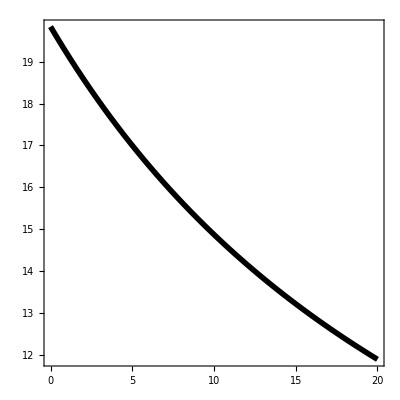

```mathematica
Plot[T2[x],{x,0,20},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,All},Frame->True,LabelStyle->{Black,20},AspectRatio->1
]
```

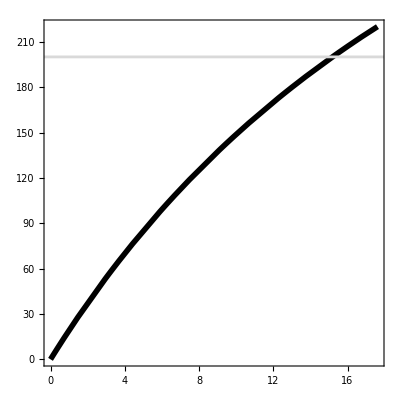

```mathematica
Plot[T2[x]*x,{x,0,300},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,{0,220}},Frame->True,LabelStyle->{Black,20},AspectRatio->1,GridLines->{{30},{200}}, GridLinesStyle->Thickness[0.005]
]
```

```mathematica
β[rat_,steep_]:= (rat)^steep/((rat)^steep+α^steep); (* When the ratio is 10:1 (1),  start eating Dreissena *)
```

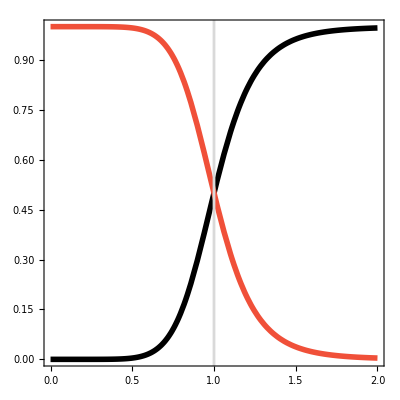

```mathematica
Show[
Plot[β[x,8]/.{α->1},{x,0,2},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
(*Plot[β[x,1]/.{α->1},{x,0,2},PlotStyle->{Black,Dashed,Thickness[0.01]},PlotRange->All],*)
Plot[1-β[x,8]/.{α->1},{x,0,2},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]},PlotRange->All],
(*Plot[1-β[x,1]/.{α->1},{x,0,2},PlotStyle->{Blue,Dashed,Thickness[0.01]},PlotRange->All],*)
Frame->True,LabelStyle->{Black,20},AspectRatio->1,AxesOrigin->{0,0},GridLines->{{1},{}}, GridLinesStyle->Thickness[0.005]
]
```

```mathematica
T2B[x_]:=((595 β[1,4])/(30+ x β[1,4]));
```

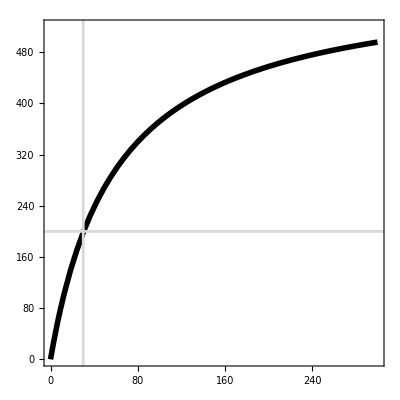

```mathematica
Plot[T2B[x]*x/.{α->1},{x,0,300},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,{0,520}},Frame->True,LabelStyle->{Black,20},AspectRatio->1,GridLines->{{30},{200}}, GridLinesStyle->Thickness[0.005]]
```

## Predator-Prey Subsystem

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,yj,fjp,δ]
```

```mathematica
PP = DynamicalSystem[{
r*V*(1 - V/kv)-(fvp/(hvp+ V))*V*P - dv V,
((yv ep)/yp)*(fvp/(hvp+ V))*V*P - dp*P
},
{{V,-0.0001,1000},{P,-0.0001,100}},
{{r,0,100},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0,1},{hvp,0,1},{fvp,0,1},{dp,0.0001,0.01},{yp,0,10000},
{kv,1,1000}
}];
PP = PP/.{r->0.1,kv->1000,dv->1/30, yv->0.67,ep->0.09,hvp->30, fvp->0.08*4900/0.67,yp->4900};
```

```mathematica
PPBD = DisplayBifurcationDiagram[PP,dp,MinStepSize->0.1,MaxSteps->200000]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,dp}={666.667,0,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,dp}={666.667,0,0.01}

-Graphics3D-

{BifurcationPoint[Branch,{0,0},{dp→0,dv→1/30,ep→0.09,fvp→585.075,hvp→30,kv→1000,r→0.1,yp→4900,yv→0.67}],BifurcationPoint[Hopf,{318.333333333333,0.0207385700113379},{dp→0.0065799043062201,dv→1/30,ep→0.09,fvp→585.075,hvp→30,kv→1000,r→0.1,yp→4900,yv→0.67}]}

```mathematica
dV = r*V*(1 - V/kv)-(fvp/(hvp+ V))*V*P - dv V;
dP = ((yv ep)/yp)*(fvp/(hvp+ V))*V*P - dp*P;
```

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
```

```mathematica
JM = {{J11,J12},{J21,J22}};
JM//MatrixForm
```

(-dv+r-(2 r V)/kv-(fvp hvp P)/(hvp+V)^2 | -(fvp V)/(hvp+V)
(ep fvp hvp P yv)/((hvp+V)^2 yp) | -dp+(ep fvp V yv)/((hvp+V) yp))

#### Feedback Level 1

```mathematica
L1 = J11+J22;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22);
```

### Plots

```mathematica
solsPP= Solve[{dV==0,dP==0},{V,P}];
```

```mathematica
solsPP
```

{{V→0,P→0},{V→(-dv kv+kv r)/r,P→0},{V→-(dp hvp yp)/(dp yp-ep fvp yv),P→-(ep hvp yv (-dp dv kv yp+dp hvp r yp+dp kv r yp+dv ep fvp kv yv-ep fvp kv r yv))/(kv (dp yp-ep fvp yv)^2)}}

```mathematica
Vp = solsPP[[2,1,2]];
Vo = solsPP[[3,1,2]];
Po = solsPP[[3,2,2]];
P0=(((yv ep)/yp)*(fvp/(hvp+ Vp))*Vp)/dp;
```

```mathematica
Pin = Solve[P0==1.0,dp][[1]][[1]][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(ep fvp kv (dv-1. r) yv)/((dv kv-1. hvp r-1. kv r) yp)

```mathematica
r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;
```

```mathematica
Pin
```

0.00688995

#### Population EQ

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->500,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

ListPlot[PPBD[[1]][[1]][[2]][[3]][[1]][[All,{1,2}]],Joined->True,PlotStyle->RGBColor["#1F449C"]],
ListPlot[MapThread[List,{PPBD[[1]][[1]][[2]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[2]][[3]][[1]][[All,3]]*5000}],Joined->True,PlotStyle->RGBColor["#F05039"]],

ListPlot[PPBD[[1]][[1]][[4]][[3]][[1]][[All,{1,2}]],Joined->True,PlotStyle->RGBColor["#1F449C"]],

ListPlot[MapThread[List,{PPBD[[1]][[1]][[4]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[4]][[3]][[1]][[All,3]]*5000}],Joined->True,PlotStyle->RGBColor["#F05039"],Frame->True,FrameTicks->{{None,All},{All,None}},FrameTicksStyle->{{None,RGBColor["#F05039"]},{Black,None}},LabelStyle->18],

FrameTicks->{{All,{{0,"0"},{100,"0.02"},{200,"0.04"},{300,"3"},{400,"4"},{500,"5"}}},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},FrameTicksStyle->{{RGBColor["#1F449C"],RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{0,250}}]
```

-Graphics-

#### Population Mean/Min/Max

```mathematica
r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;
```

```mathematica
min = 0.001; max =0.0064; gran = 0.0001;
Vpeaks1 = List[];
Vmeans1 = List[];
Vvalleys1 = List[];
Pvalleys1 = List[];
Ppeaks1 = List[];
Pmeans1 = List[];
```

```mathematica
Clear[i];
lastV = 0.1;
lastP = 0.001;
For[i=(min/gran),i<=(max/gran),i++,
dp = i*gran;
TS=NDSolveValue[
{ V'[t]==r*V[t]*(1 - V[t]/kv)-(fvp/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*(fvp/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],

V[0]==0.1,P[0]==0.001
},{V,P},{t,0,100000},MaxStepSize->0.1];

Tout = Table[Evaluate[#[t]& /@TS],{t,50000,100000}];
peaks = FindPeaks[Tout[[All,1]], Automatic, Automatic, 0.1];

If[Length[peaks]>1,
per = Tout[[peaks[[-2]][[1]];;peaks[[-1]][[1]]]];
AppendTo[Vpeaks1,{i*gran,Max[per[[All,1]]]}];
AppendTo[Vvalleys1,{i*gran,Min[per[[All,1]]]}];
AppendTo[Vmeans1,{i*gran,Mean[per[[All,1]]]}];
AppendTo[Ppeaks1,{i*gran,Max[per[[All,2]]]}];
AppendTo[Pvalleys1,{i*gran,Min[per[[All,2]]]}];
AppendTo[Pmeans1,{i*gran,Mean[per[[All,2]]]}],

AppendTo[Vpeaks1,{i*gran,Tout[[All,1]][[-1]]}];
AppendTo[Vvalleys1,{i*gran,Tout[[All,1]][[-1]]}];
AppendTo[Vmeans1,{i*gran,Tout[[All,1]][[-1]]}];
AppendTo[Ppeaks1,{i*gran,Tout[[All,2]][[-1]]}];
AppendTo[Pvalleys1,{i*gran,Tout[[All,2]][[-1]]}];
AppendTo[Pmeans1,{i*gran,Tout[[All,2]][[-1]]}];
];

lastV = per[[All,1]][[-1]];
lastP = per[[All,2]][[-1]];
]
```

```mathematica
min = 0.006405; max =0.00658; gran = 0.000005;
Vpeaks2 = List[];
Vmeans2 = List[];
Vvalleys2 = List[];
Pvalleys2 = List[];
Ppeaks2 = List[];
Pmeans2 = List[];
```

```mathematica
Clear[i];
lastV = 0.1;
lastP = 0.001;
For[i=(min/gran),i<=(max/gran),i++,
dp = i*gran;
TS=NDSolveValue[
{ V'[t]==r*V[t]*(1 - V[t]/kv)-(fvp/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*(fvp/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],

V[0]==0.1,P[0]==0.001
},{V,P},{t,0,100000},MaxStepSize->0.01];

Tout = Table[Evaluate[#[t]& /@TS],{t,50000,100000}];
peaks = FindPeaks[Tout[[All,1]], Automatic, Automatic, 0.1];

If[Length[peaks]>1,
per = Tout[[peaks[[-2]][[1]];;peaks[[-1]][[1]]]];
AppendTo[Vpeaks2,{i*gran,Max[per[[All,1]]]}];
AppendTo[Vvalleys2,{i*gran,Min[per[[All,1]]]}];
AppendTo[Vmeans2,{i*gran,Mean[per[[All,1]]]}];
AppendTo[Ppeaks2,{i*gran,Max[per[[All,2]]]}];
AppendTo[Pvalleys2,{i*gran,Min[per[[All,2]]]}];
AppendTo[Pmeans2,{i*gran,Mean[per[[All,2]]]}],

AppendTo[Vpeaks2,{i*gran,Tout[[All,1]][[-1]]}];
AppendTo[Vvalleys2,{i*gran,Tout[[All,1]][[-1]]}];
AppendTo[Vmeans2,{i*gran,Tout[[All,1]][[-1]]}];
AppendTo[Ppeaks2,{i*gran,Tout[[All,2]][[-1]]}];
AppendTo[Pvalleys2,{i*gran,Tout[[All,2]][[-1]]}];
AppendTo[Pmeans2,{i*gran,Tout[[All,2]][[-1]]}];
];

lastV = per[[All,1]][[-1]];
lastP = per[[All,2]][[-1]];
]
```

```mathematica
FinalV = Join[Vmeans1, Vmeans2, PPBD[[1]][[1]][[2]][[3]][[1]][[All,{1,2}]]];
FinalP = Join[MapThread[List,{Pmeans1[[All,1]],Pmeans1[[All,2]]*5000}], MapThread[List,{Pmeans2[[All,1]],Pmeans2[[All,2]]*5000}],MapThread[List,{PPBD[[1]][[1]][[2]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[2]][[3]][[1]][[All,3]]*5000}]];
```

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-1000,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-1000,1000}, BoundaryStyle->{Gray},PlotPoints->500,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

ListPlot[Vvalleys1,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dotted,Thickness[0.01]}],
ListPlot[Vvalleys2,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dotted,Thickness[0.01]}],
ListPlot[FinalV,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListPlot[Vpeaks1, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],
ListPlot[Vpeaks2, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListPlot[MapThread[List,{Pvalleys1[[All,1]],Pvalleys1[[All,2]]*5000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dotted,Thickness[0.01]}],
ListPlot[MapThread[List,{Pvalleys2[[All,1]],Pvalleys2[[All,2]]*5000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dotted,Thickness[0.01]}],
ListPlot[FinalP,Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListPlot[MapThread[List,{Ppeaks1[[All,1]],Ppeaks1[[All,2]]*5000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListPlot[MapThread[List,{Ppeaks2[[All,1]],Ppeaks2[[All,2]]*5000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,FrameTicks->{{All,{{0,"0"},{100,"0.02"},{200,"0.04"},{300,"0.06"},{400,"0.08"},{500,"0.10"},{600,"0.12"},{700,"0.14"}}},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},FrameTicksStyle->{{RGBColor["#1F449C"],RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0.001,0.0072},{-1,700}}]
```

-Graphics-

```mathematica
Show[
LogPlot[x=-1,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-1000,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-1000,1000}, BoundaryStyle->{Gray},PlotPoints->500,PlotStyle->LightYellow],


ListLogPlot[Vvalleys1,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dotted,Thickness[0.01]}],
ListLogPlot[Vvalleys2,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dotted,Thickness[0.01]}],
ListLogPlot[FinalV,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks1, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],
ListLogPlot[Vpeaks2, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys1[[All,1]],Pvalleys1[[All,2]]*5000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dotted,Thickness[0.01]}],
ListLogPlot[MapThread[List,{Pvalleys2[[All,1]],Pvalleys2[[All,2]]*5000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dotted,Thickness[0.01]}],
ListLogPlot[FinalP,Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks1[[All,1]],Ppeaks1[[All,2]]*5000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Ppeaks2[[All,1]],Ppeaks2[[All,2]]*5000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,AxesOrigin->{0,-10},FrameTicksStyle->{{RGBColor["#1F449C"],RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0.001,0.0072},{-2,7}}]
```

-Graphics-

#### Invert Density Dependence

```mathematica
IDD = FullSimplify[D[dV/V,V]];
```

```mathematica
IDD
```

-r/kv+(fvp P (V/M)^ω (V (V/M)^ω-hvp α^ω ω))/(V ((V/M)^ω (hvp+V)+hvp α^ω)^2)

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->200,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[IDD/.{V->Vo,P->Po},{dp,0.0001,0.006889}, PlotStyle->RGBColor["#1F449C"]],
FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.0005,0.0022}}]
```

-Graphics-

#### Loop Dissection

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->200,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[L1/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L2/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.01,0.04}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.006889 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->200,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.00658 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->200,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[J11/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[J22/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[L1/.{V->Vo,P->Po},{dp,0.0001,0.0069},PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

FrameTicks->{{All,None},{{{0.000,"0.000"},0.002,0.004,0.006,0.008},None}},
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.0001,0.0072},{-0.01,0.04}}]
```

-Graphics-